# Fully implicit scheme for ac voltammetry

## Using expanding space grid

Version 2.0
copyright © 2002-Year Michael Honeychurch

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
xTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

yTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4//N}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4//N}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20//N}]];

xTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];

yTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],Ceiling[max]/4}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-Ceiling[max]/4}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],Ceiling[max]/20}]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.5]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
(*options for voltammograms*)
optionA={
PlotRange:>{{0,n},{Min[acv1]-0.1,Max[acv1]+0.1}},
FrameTicks-> {Automatic,yTicks2,Automatic,yTicks4},
PlotStyle->{Red,AbsoluteThickness[0.7]},
FrameLabel->{
Style["increment",FontFamily->"Arial" ,FontSize-> 12,FontColor->Black],
Style["χ",FontFamily-> "Times New Roman" ,FontSize->  12, FontWeight->  "Plain",FontColor->Black],
None,
None}
};
```

```mathematica
(*options for voltammograms*)
optionB={
PlotStyle-> {Red,AbsoluteThickness[0.7]},
FrameTicks:>  {xTicks1,yTicks2,xTicks3,yTicks4},
FrameLabel->{
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],
Style["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}
};
```

```mathematica
(*options for power spectrum plots*)
optionMain={
PlotStyle->{Black,AbsoluteThickness[0.7]},
FrameTicks->Automatic,
FrameLabel->{"Frequency / π",None,None,None},
DisplayFunction->Identity};
```

```mathematica
(*options for power spectrum plots*)
optionInset={
PlotStyle->{Black,AbsoluteThickness[0.7]},
FrameTicks->Automatic,
PlotRange->{{(2*Ω/Pi)-2,(2*Ω/Pi)+2},{0,0.12}},
BaseStyle->{FontSize->7},
FrameLabel->{"Frequency / π",None,None,None},
DisplayFunction->Identity};
```

```mathematica
dcOptions={
Joined-> True,
PlotStyle->{Red,Thickness[0.003]},
FrameTicks-> Automatic,
FrameLabel-> {
Style["nF/RT(E-E°)",FontFamily-> "Times New Roman",FontSize-> 12, FontSlant->Italic],
Style["√πχ",FontFamily-> "Times New Roman",FontSize-> 12, FontWeight-> "Plain"],
None,
None}
};
```

```mathematica
$Line=0;
```

## Make Diagonals

```mathematica
Clear[makeVarDiagonals2];

makeVarDiagonals2[m_Integer,d_][a_]:=
	Module[{x,y,z},
		x=Table[-d*a^(4-2*j),{j,3,m-1}];(*lower diagonal*)
		z=Table[-d*a^(3-2*j),{j,2,m-2}];(*upper diagonal*)
		y=Table[1+(1+a)*d*a^(3-2*j),{j,2,m-1}];(*centre*)
{x,y,z}]
```

```mathematica
Clear[𝔻,a,x,y,z];
{x,y,z}=makeVarDiagonals2[7,𝔻][a]
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,4},{j,4}]//MatrixForm
```

{{-𝔻/a^2,-𝔻/a^4,-𝔻/a^6,-𝔻/a^8},{1+((1+a) 𝔻)/a,1+((1+a) 𝔻)/a^3,1+((1+a) 𝔻)/a^5,1+((1+a) 𝔻)/a^7,1+((1+a) 𝔻)/a^9},{-𝔻/a,-𝔻/a^3,-𝔻/a^5,-𝔻/a^7}}

(1+((1+a) 𝔻)/a | -𝔻/a | 0 | 0
-𝔻/a^2 | 1+((1+a) 𝔻)/a^3 | -𝔻/a^3 | 0
0 | -𝔻/a^4 | 1+((1+a) 𝔻)/a^5 | -𝔻/a^5
0 | 0 | -𝔻/a^6 | 1+((1+a) 𝔻)/a^7)

## Set Up Solution

```mathematica
Clear[implicitSolveIrrevExpAC];

implicitSolveIrrevExpAC[m_Integer,n_Integer,d_,{lowerLimit_,upperLimit_},{ksStar_,α_},{Δ𝔼_,Ω_},a_]:=Module[{x,y,z,len,mat,y1,z1,initial,range,τ,solveNext},

range=(upperLimit+Abs[lowerLimit]);
τ=range/(n-1.);

{x,y,z}=makeVarDiagonals2[m,d][a];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
y1=y⟦1⟧;
z1=z⟦1⟧;
initial=ConstantArray[1.,{m}];

solveNext[list_List,k_Integer]:=Module[{tmp,ξ,b,tmp2,tmp3},

ξ=Exp[upperLimit-(τ*(k-1))-Δ𝔼*Sin[Ω*(k-1)*τ]];
tmp=ξ^α/(3.*ξ^α+ ksStar*(1.+ξ));

b=list[[2;;-2]];
b⟦1⟧+=(tmp*d*ksStar*ξ^(1.-α));
b⟦-1⟧+=d*a^(5-2*m);
mat⟦1,1⟧=y1-4.*d*tmp;
mat⟦1,2⟧=z1+d*tmp;
tmp2=LinearSolve[mat,b];
tmp3=Flatten[{(ksStar*ξ^(1.-α)+4.*tmp2⟦1⟧-tmp2⟦2⟧)*tmp,tmp2,1.}]
(*Take[tmp3,3]*)
];

FoldList[solveNext,initial,Range[2,n]]
]
```

## Set Parameter Values

### Variables/ constants

```mathematica
Clear[F,R,T,f,𝒟];

F=N@QuantityMagnitude[UnitConvert@Quantity["FaradayConstant"]];(*Faradays constant*)

R=N@QuantityMagnitude[UnitConvert@Quantity["GasConstant"]];(*gas constant*)

T=298.15;(*temperature*)
f=F/(R*T);
𝒟=1.*^-5;(*diffusion coefficient*)
```

### Electrochemical variables

```mathematica
Clear[α,υ,ks,Δ𝔼,Ω,upperLimit,lowerLimit,region,σ,ω,cycles]

α=0.5;

υ=-1.(*sweep rate V/s*);

ks=1.*^3(*standard rate constant*);

Δ𝔼=f*0.005 ;(*dimensionless AC amplitude = f × amplitude in V*)

Ω=6.4*Pi; (*dimensionless frequency*)

lowerLimit=-10.(*limit = f×(E-E^o)*);

upperLimit=10.(*limit = f×(E-E^o)*);

region=(upperLimit+Abs[lowerLimit]);

σ=f*υ;

ω=Ω*f*Abs[υ]; (*calculation of the dimensional angular frequency*)

cycles=Abs[region*Ω/(2*Pi)];
```

### Simulation variables

```mathematica
Clear[n,a,𝔻,temp,m,τ,time,ksStar];

n=2^12;

a=1.2;

𝔻=2.;

temp=Solve[∑_(j=1)^(mm-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),mm,InverseFunctions-> True];

m=mm/.temp⟦1⟧//Ceiling;(*number of spacial grid points*)

τ=region/(n-1);(*calculation of the incremental time/potential step*)

time=Abs[region/σ];

ksStar=2.ks*Sqrt[time/(𝒟*𝔻*(n-1))];(*dimensionless rate constant*)
```

## Solve

```mathematica
c=implicitSolveIrrevExpAC[m,n,𝔻,{lowerLimit,upperLimit},{ksStar,α},{Δ𝔼,Ω},a];//Timing
```

{1.01265,Null}

## Plot ac voltammogram

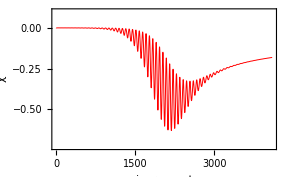

```mathematica
acv1=(((2+a) a #1⟦1⟧-(1+a)^2 #1⟦2⟧+#1⟦3⟧) √((𝔻 (n-1))/(2 a^2 (1+a) region))&)/@c;
plot1=ListPlot[acv1,optionA,PlotRange->{{0,n},{Min[acv1]-0.1,Max[acv1]+0.1}}]
```

```mathematica
convert[i_,{j_}]:={upperLimit-(τ*j),i}
```

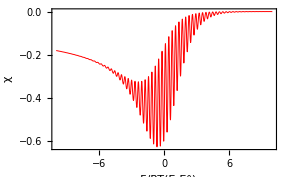

```mathematica
acv2=MapIndexed[convert,acv1];

plot2=ListPlot[acv2,optionB]
```

## Moving average filter

Filter data with a moving average filter to remove ac component then re-plot data. If necessary repeat the filtering a second time. The moving average filter averages over N points with N being the number of increments per cycle. Round is used to convert n/cycles from a real number into an integer.

```mathematica
data2=MovingAverage[acv1,Round[n/cycles]];
data2=MovingAverage[data2,Round[n/cycles]];
```

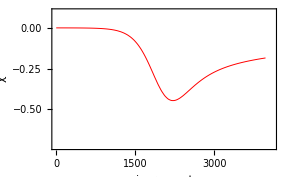

```mathematica
plot3=ListPlot[data2,optionA]
```

The moving average chops the data list. To subtract the unfiltered data, acv1, from the filtered data, data2, we need to align the lists. We do this by first determining the length of the over hang.

```mathematica
Clear[xx];
xx=Length[acv1]-Length[data2]
```

126

```mathematica
convert2[i_,{j_}]:={upperLimit-(xx*τ/2.)-(τ*j),i}
```

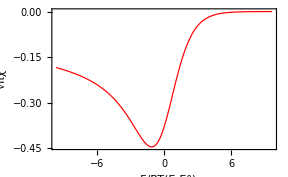

```mathematica
acv3=MapIndexed[convert2,data2];

plot2=ListPlot[acv3,dcOptions]
```

The peak height and peak position are now obtained. Better accuracy is obtained by increasing the magnitude of n.

```mathematica
peakHeight=Min[acv3⟦All,2⟧];
Select[acv3,#⟦2⟧==peakHeight&]//Flatten;
Print["peak at ",%⟦1⟧*1000/f," mV with height ",peakHeight]
```

peak at -28.7983 mV with height -0.445724

## Fourier transform filter

```mathematica
cycles=Abs[region*Ω/(2*Pi)];
Print["The frequency is ",ω]
Print[noCycles=Round[cycles]," oscillations of width ",region/cycles," Each oscillation contains ",incrPerCycle=n/cycles, " increments"]
```

The frequency is 782.568

64 oscillations of width 0.3125 Each oscillation contains 64. increments

```mathematica
powerSpectrum[a_,{b_}]:={(b-1)*Ω/(noCycles*Pi),a}
```

```mathematica
fourierData=Abs[Fourier[acv1]];
fourierData=MapIndexed[powerSpectrum,fourierData];
peak=Select[fourierData,(#⟦1⟧==Ω/π)&];
pRange={PlotRange:> {{1,Ceiling[3*Ω/π]},{0,Ceiling[peak⟦1,2⟧]+1}}};
```

```mathematica
DynamicModule[{pt=Scaled[{0.65,0.5}]},
ListPlot[fourierData,optionMain,pRange,
PlotRange->All,
Epilog->{Dynamic[Locator[Dynamic[pt],ListPlot[fourierData,optionInset,Background->None,ImageSize->150]]]}
]
]
```

```mathematica
Clear[fourierFilter];

fourierFilter[list_List,x_Integer,y_Integer]:=Module[{a,b},
a=Fourier[list];b=Join[Table[0,{j,1,x-1}],Table[a⟦j⟧,{j,x,y}],Table[0,{j,1,Length[a]-(2*(y+1))}],Table[a⟦j⟧,{j,Length[a]-(y+1),Length[a]-(x-1)}],Table[0,{j,1,x-1}]];Re[InverseFourier[b]]];
```

Convert from dimensionless linear sweep to dimensionless ac by multiplying by 1/(Δ E)√(υ/ω)

#### 1st Harmonic

```mathematica
newdata=fourierFilter[acv1,(noCycles+1)-12,(noCycles+1)+12]*Sqrt[Abs[f*υ]/ω]/Δ𝔼;

(*add dimensionless potential scale to the x axis*)

firstHarmonic=MapThread[{#1⟦1⟧,#2}&,{acv2,newdata}];
```

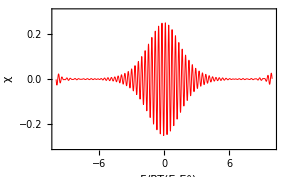

```mathematica
firstHarmonicPlot=ListPlot[firstHarmonic,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata]-0.05,Max[newdata]+0.05}}]
```

#### 2nd Harmonic

```mathematica
newdata2=fourierFilter[acv1,((2*noCycles)+1)-11,((2*noCycles)+1)+11];

(*add dimensionless potential scale to the x axis*)

secondHarmonic=MapThread[{#1⟦1⟧,#2}&,{acv2,newdata2}];
```

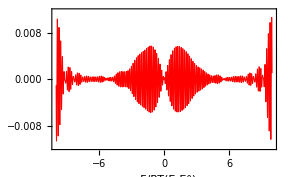

```mathematica
secondHarmonicPlot=ListPlot[secondHarmonic,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata2]-0.001,Max[newdata2]+0.001}}]
```

#### 3rd Harmonic

```mathematica
newdata3=fourierFilter[acv1,((3*noCycles)+1)-11,((3*noCycles)+1)+11];

(*add dimensionless potential scale to the x axis*)

thirdHarmonic=MapThread[{#1⟦1⟧,#2}&,{acv2,newdata3}];
```

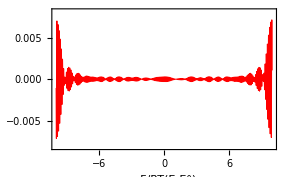

```mathematica
thirdHarmonicPlot=ListPlot[thirdHarmonic,optionB,PlotRange->{{lowerLimit,upperLimit},{Min[newdata3]-0.001,Max[newdata3]+0.001}}]
```

#### DC component

```mathematica
newdata4=fourierFilter[acv1,1,53];

(*add dimensionless potential scale to the x axis*)

dcComponent=MapThread[{#1⟦1⟧,#2}&,{acv2,newdata4}];
```

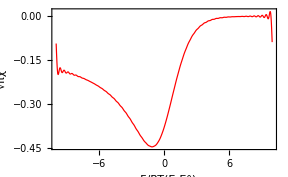

```mathematica
dcComponentPlot=ListPlot[dcComponent,dcOptions]
```